```mathematica
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
```

## Misc Modules

```mathematica
eps = 10^-6;
```

```mathematica
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)](* range btwn 10^a and 10^b *)
```

```mathematica
logspace[-1,2,4]
```

{0.1,1.,10.,100.}

```mathematica
logspace2[a_,b_,n_,d_]:=d^Range[Log[d,a],Log[d,b],(Log[d,b]-Log[d,a])/(n-1)]
```

```mathematica
logspace2[0.1,100,4,200.]
```

{0.1,1.,10.,100.}

```mathematica
cosExpansion[x_]:=1-x^2/2+x^4/24-x^6/720;
```

```mathematica
stripList[lst_]:=Module[{lst2},
lst2 = List[];
Do[AppendTo[lst2,Last[lst[[ii]]]],{ii,Length[lst]}];
Return[lst2]]
```

```mathematica
a=List[{1},{2},{3}]
stripList[a]
```

{{1},{2},{3}}

{1,2,3}

```mathematica
(* Write Module to Count number of roots in a function *)
(* From https://www.physicsforums.com/threads/find-all-roots-of-an-interpolating-function-in-mathematica.612362/ *)
countZeros[ifun_,xmin_,xmax_,dx_] := Module[{zeros,numZeros},
zeros = Union[Table[x/.FindRoot[ifun[x]==0.,{x,xInit,xmin,xmax}],{xInit,xmin+dx,xmax-dx,dx}],SameTest->(Abs[#1-#2]<10^-4&)];
numZeros = Length[zeros];
(*Print[zeros];*)
If[Last[zeros]==xmax,If[ifun[xmax]≠0,numZeros=numZeros-1]];
If[First[zeros]==xmin,If[ifun[xmin]≠0,numZeros=numZeros-1]];
Return[numZeros]]
```

```mathematica
f[x_]:=x^4-x^2
countZeros[f,-2,2,0.1]
```

3

```mathematica
countAllZeros[ifun_,xmin_,xmax_,dx_,hardLim_]:=Module[{z,ztot,num,ii},
z=countZeros[ifun,xmin,xmax,dx];
Print["number of zeros for the function is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[x_]=D[ifun[x],{x,ii}];
If[f[x_]==0,Break[]];
z=countZeros[f,xmin,xmax,dx];
Print["number of zeros for ",ii,"th derivative is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
f[x_]:=x^4-x^2
countAllZeros[f,-10,10,0.1,1]
```

number of zeros for the function is 3

number of zeros for 1th derivative is 3

6

```mathematica
inflectionShift[fun_,funpp_]:=Module[{fun2,xi},
xi = Min[x/.NSolve[funpp[x]==0,x]];
fun2[x_]=fun[x+xi];
Return[fun2]]
```

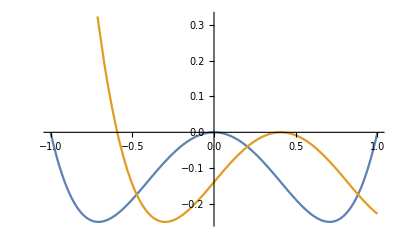

```mathematica
f[x_]:=x^4-x^2;
f2=inflectionShift[f,f''];
Plot[{f[x],f2[x]},{x,-1,1}]
```

```mathematica
vacuumShift[fun_]:=Module[{vac,fun2},
vac = Minimize[fun[x],x];
fun2[x_]=fun[x]-vac[[1]];
Return[fun2]]
```

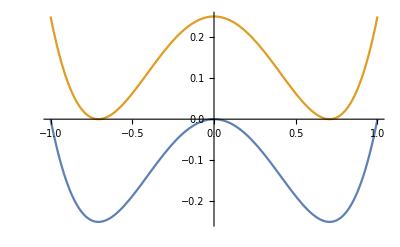

```mathematica
f[x_]:=x^4-x^2;
f2=vacuumShift[f];
Plot[{f[x],f2[x]},{x,-1,1},PlotRange->Full]
```

```mathematica
SolveVolterraEqn[g_,x0_,y_,xmax_]:=Module[{x1,y1,nn},
(* Solve y = ∫_x0^x1 g[x]ⅆx for x1 in the range x0 to xmax *)
(* Works for going either left or right (dending on if x0>or<xmax *)
nn = 1;
x1 = x0+(xmax-x0)/2^nn;
While[True,
y1 = NIntegrate[g[x],{x,x0,x1}];
If[Abs[y1-y]<eps,Break[]];
nn = nn+1;
If[y1>y,x1 = x1 -(xmax-x0)/2^nn;,
x1 = x1 +(xmax-x0)/2^nn;];
];
Return[x1]]
```

```mathematica
v[x_]:=(0.01)*((x^2-(10)^2)^2 );
g[x_]=v[x]/v'[x];
SolveVolterraEqn[g,8.6,80,0]
```

0.24226

```mathematica
v[x_]:=(0.1)*(1+Log[x]+0.001*x^4);
g[x_]=v[x]/v'[x];
SolveVolterraEqn[g,0.8,80,100]
```

20.9486

## Cosmology Calculation Modules

```mathematica
findZϵsr[v_,vp_,ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{ϵsr,f,z,num,ii,ztot},
ϵsr[x_]:=1/2*(vp[x]/v[x])^2;
f[n_]:=ϵsr[ϕ[n]]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ϵsr"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ϵsr is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ϵsr[ϕ[n]]/.ϕsol,{n,ii}];
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of ϵ is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findZϵ[v_,ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{hsq,ϵ,f,z,num,ii,ztot},
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
ϵ[n_] = Evaluate[3*ϕ'[n]^2/(ϕ'[n]^2+2*v[ϕ[n]]/hsq[n])];
f[n_] = ϵ[n]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ϵ"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ϵ is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ϵ[ϕ[n]],{n,ii}]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of ϵ is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findZη[v_,vpp_,ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{ηsr,f,z,num,ii,ztot},
ηsr[n_]:=vpp[ϕ[n]]/v[ϕ[n]];
f[n_]:=ηsr[ϕ[n]]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ηsr"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ηsr is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ηsr[ϕ[n]]/.ϕsol,{n,ii}];
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of η is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findH[v_]:=Module[{h,hsq},
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
Return[{h,hsq}]]
```

### Find Initial Conditions for 1st Integration

```mathematica
chooseϕ0Manual[ϕ0list_]:=Module[{ϕ0index,ϕ0},
ϕ0index = Input["Enter the index for the ϕ0 you want to use: \n(Counting starts at 1)"];
ϕ0 = ϕ0list[[ϕ0index]]; 
Return[ϕ0]]
```

```mathematica
chooseϕ0Left[ϕ0list_,v_]:=Module[{ϕ0listpos,ϕ0,vacuumArray},
ϕ0listpos=Select[ϕ0list,#>0&];
(* vacuum = First[Select[ϕ0listpos,v[#]<10^-6&]];
ϕ0 = Max[Select[ϕ0listpos,#<vacuum&]]; *)
If[ϕ0listpos=={},
vacuumArray =Select[ϕ0list,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Min[ϕ0list],
ϕ0 = Min[Select[ϕ0list,#<First[vacuumArray]&]]];,
(*else*)
vacuumArray =Select[ϕ0listpos,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Min[ϕ0listpos],
ϕ0 = Max[Select[ϕ0listpos,#<First[vacuumArray]&]]];
];
Return[ϕ0]]
```

```mathematica
chooseϕ0Right[ϕ0list_,v_]:=Module[{ϕ0listpos,ϕ0,vacuumArray},
ϕ0listpos=Select[ϕ0list,#≥0&];
If[ϕ0listpos=={},
vacuumArray =Select[ϕ0list,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Max[ϕ0list],
ϕ0 = Max[Select[ϕ0list,#>First[vacuumArray]&]]];,
(* else *)
vacuumArray =Select[ϕ0listpos,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Max[ϕ0listpos],
ϕ0 = Min[Select[ϕ0listpos,#>First[vacuumArray]&]]];
];
Return[ϕ0]]
```

```mathematica
guessϕiLeft[v_,vpp_,ni_,ϕ0_]:=Module[{guesses,ϕiguess},
guesses = t/.NSolve[ni==v[t]/vpp[t],t];
Print["guesses = ",guesses];
ϕiguess=Min[Select[guesses,#>0&&#<ϕ0&]];
Return[ϕiguess]]
```

```mathematica
guessϕiRight[v_,vpp_,ni_,ϕ0_]:=Module[{guesses,ϕiguess},
guesses = t/.NSolve[ni==v[t]/vpp[t],t];
Print["guesses = ",guesses];
ϕiguess=Min[Select[guesses,#>0&&#>ϕ0&]];
Return[ϕiguess]]
```

```mathematica
findICsr[v_,vp_,vpp_,ni_,plots_,prints_,left_]:=Module[{ϕ0list,ϕ0index,ϕ0,f,g,ϕiguess,ϕi1s,ϕi1,ϕpi1,vplt,ϕ0plt,ϕiplt,ϕi1sol,ϕmax},
vplt = Plot[v[x],{x,-5,12},AxesLabel->{"ϕ","V"},PlotRange->Full];
(* Solve for where ϵ=1 and hence N=0 *)
ϕ0list = Normal[NSolve[vp[x]==√2*v[x],x,Reals]]/.C[1]->0;
ϕ0list = Values[stripList[Union[ϕ0list,Normal[NSolve[vp[x]==-√2*v[x],x,Reals]]/.C[1]->0]]];
Print["ϕ0list = ",ϕ0list];
If[plots,ϕ0plt = ListPlot[Transpose[{ϕ0list,v[ϕ0list]}]]; (* Transpose is Zip!! *)
Print[Show[vplt,ϕ0plt]]];
If[left,ϕ0 = chooseϕ0Left[ϕ0list,v],ϕ0 = chooseϕ0Right[ϕ0list,v]];
If[prints,Print["ϕ0 = ",ϕ0]];
If[ϕ0==∞,Print["ϕ0=∞"];Abort[]];
If[ϕ0==-∞,Print["ϕ0=-∞"];Abort[]];
(* Integrate up the hill to find the value of ϕ at ni *)
Clear[x,t];
(* f[t_] := Integrate[v[x]/vp[x],{x,ϕ0,t}];
If[prints,Print["f[t] = ",f[t]]]; 
If[left,ϕi1s = t/.NSolve[ni==f[t]&&t≥0 && t≤ϕ0,t];,
ϕi1s = t/.NSolve[ni==f[t]&&t≥0 && t≥ϕ0,t]];
If[prints,Print["ϕi1s = NSolve[ni==f[t]] = ",ϕi1s]];
If[ϕi1s==t,Abort[]];
ϕi1 = Last[ϕi1s]; *)
g[x_]=v[x]/vp[x];
If[left,ϕmax=0,ϕmax=50];
ϕi1 = SolveVolterraEqn[g,ϕ0,ni,ϕmax];
ϕpi1 = vp[ϕi1]/v[ϕi1] ;
If[True,ϕiplt = ListPlot[{{ϕi1,v[ϕi1]},{ϕ0,v[ϕ0]}}];
Print[Show[vplt,ϕiplt]]];
Return[{ϕi1,ϕpi1}]]
```

### Find Initial Conditions for 2nd Integration

```mathematica
findICshifted[v_,ϕsol1_,ni_,nf_,ni2_,n1guess_,prints_,plots_]:=Module[{ϵ1,n1,ϕi2,ϕpi2,roots},
(* Find ϵ1 *)
ϵ1=findϵ[v,ϕsol1];
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ1[n]/.n->0]]];
If[plots,Print[Plot[Evaluate[ϵ1[n]],{n,nf,ni},AxesLabel->{N,"ϵ1"},PlotRange->{{nf,-nf},{0,2}},GridLines->{{-1,-1.2},{1}}]]];
(* Solve for where ϵ1[n]==1 *)
roots = Check[FindRoot[ϵ1[n]-1,{n,n1guess}],"1/0 Error",Power::infy];
Print["roots = ",roots];
If[roots=="1/0 Error",Print["THROW!"];Throw["n1 = 1/0"]];
n1 = Evaluate[n/.First[roots]];
If[prints,Print["At n1 = ",n1,", ϵ1 = ",Evaluate[ϵ1[n]/.n->n1]]];
If[n1==n1guess, Abort[]];
(* Find the new initial conditions *)
ϕi2 = Re[ϕ[ni2+n1]/.ϕsol1];
If[prints,Print["ϕi2 = ",ϕi2]];
ϕpi2 = Re[D[ϕ[n],n]/.ϕsol1/.n->(ni2+n1)];
If[prints,Print["ϕpi2 = ",ϕpi2]];
Return[{ϕi2,ϕpi2}]]
```

```mathematica
solveKG[hsq_,vp_,ni_,nf_,ϕi1_,ϕpi1_,plots_]:=Module[{ϕsol1},
ϕsol1 = Last@Last@NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[ni]==ϕi1,ϕ'[ni]==ϕpi1},ϕ,{n,ni,nf},InterpolationOrder->All];
If[plots,Print[Plot[Evaluate[ϕ[n]/.ϕsol1],{n,nf,ni},AxesLabel->{N,"ϕsol"},GridLines->{{-1,-1.2},{1}}]]];
Return[ϕsol1]]
```

### Find Epsilon

```mathematica
findϵ[v_,ϕsol_]:=Module[{ϕp,hsq,ϵ,η},
ϕp[n_] = D[ϕ[n],n]/.ϕsol;
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕp[n]^2)/.ϕsol;
ϵ[n_] = Evaluate[3*ϕp[n]^2/(ϕp[n]^2+2*v[ϕ[n]]/hsq[n])/.ϕsol];
(* above took out a Re[] just inside the Evaluate[] *)
(* η[n_] = D[ϵ[n],n]; *)
Return[ϵ]]
```

```mathematica
findϕsol[v_,vp_,vpp_,ni_,nf_,ni2_,nf2_,n1guess_,plots_,prints_,left_]:=Module[{h,hsq,ϕi1,ϕpi1,ϕsol1,ϕi2,ϕpi2,ϕsol2},
(* Define the hubble parameter *)
{h,hsq}=findH[v];
(* Find the slow roll initial conditions *)
{ϕi1,ϕpi1}=findICsr[v,vp,vpp,ni,plots,prints,left];
(* Solve the Klein-Gordon equation for ϕ1[n] *)
ϕsol1 = solveKG[hsq,vp,ni,nf,ϕi1,ϕpi1,plots];
(* Find the new initial conditions and re-solve the KG equation *)
{ϕi2,ϕpi2}=findICshifted[v,ϕsol1,ni,nf,ni2,n1guess,prints,plots];
ϕsol2 = solveKG[hsq,vp,ni2,nf2,ϕi2,ϕpi2,plots];
(* Note: before I had it integrating from nf2 to ni2 *)
If[prints,Print["ϕsol2[60] = ",ϕ[60]/.ϕsol2]];
Return[ϕsol2]]
```

```mathematica
findϕsolnfLoop[v_,vp_,vpp_,ni_,nf_,ni2_,nf2_,n1guess_,plots_,prints_,left_,nfStep_]:=Module[{nff,ϕsol2},
nff=nf;
While[nff<-eps,
ϕsol2=Block[{Print},Quiet[Catch[findϕsol[v,vp,vpp,ni,nff,ni2,nf2,n1guess,False,False,left]]]];
If[ϕsol2==="n1 = 1/0",Print["."];nff=nff+nfStep,Break[]];
];
Print["nff = ",nff];
If[plots||prints,ϕsol2=Catch[findϕsol[v,vp,vpp,ni,nff,ni2,nf2,n1guess,plots,prints,left]]];
Return[ϕsol2]]
```

```mathematica
findNsR[v_,vp_,ϕsol2_,ni2_,nf2_,plots_,prints_] := Module[{ϕ2p,h2sq,ϵ2,ns,r,ϵsr,ϵsrL,ηsr,ηsrL,Zϵ,Zη },
(* Find ϵ2 *)
ϵ2 = findϵ[v,ϕsol2];
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ2[n]/.n->0]]];
If[plots,Print[Plot[Evaluate[ϵ2[n]],{n,nf2,ni2},AxesLabel->{N,"ϵ2"},PlotRange->{{nf2,ni2},{0,1}}]]];
(* Find the spectral tilt: ns[n] *)
ns[n_] := 1-2*ϵ2[n]+D[Log[ϵ2[n]],n];
If[prints,Print["ns[60] = ",ns[n]/.{n->60}]];
r[n_] := 16*ϵ2[n];
If[prints,Print["r[60] = ",r[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[ns[n]],{n,nf2,ni2},AxesLabel->{N,"ns"}]]];
Return[{ns[n],r[n],ϵ2}]];
```

```mathematica
findSRparams[v_,vp_,vpp_,ϕsol2_,ni2_,nf2_,prints_,plots_]:=Module[{ϵsr,ϵsrL,ηsr,ηsrL},
(* Find slow roll params ϵsr and ηsr *)
ϵsr[n_]:=1/2*(vp[ϕ[n]]/v[ϕ[n]])^2/.ϕsol2;
ϵsrL[n_]:=1/2*D[Log[v[ϕ[n]]],n]/.ϕsol2;
If[prints,Print["ϵsr[0] = ",ϵsr[n]/.{n->0}]];
If[prints,Print["ϵsr[60] = ",ϵsr[n]/.{n->60}]];
If[prints,Print["ϵsrL[0] = ",ϵsrL[n]/.{n->0}]];
If[prints,Print["ϵsrL[60] = ",ϵsrL[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[1/2*(vp[x]/v[x])^2],{x,0,30},AxesLabel->{"ϕ","ϵ[ϕ]"},PlotRange->{0,10}]]];
If[plots,Print[Plot[{Legended[Evaluate[ϵsr[n]],"ϵsr"],Legended[ϵ2[n],"ϵ2"],Legended[Evaluate[ϵsrL[n]],"ϵsrL"]},{n,nf2,ni2},AxesLabel->{N,"ϵsr"},PlotRange->{{nf2,ni2},{0,3}}]]];
ηsr[n_]:=vpp[ϕ[n]]/v[ϕ[n]]/.ϕsol2;
ηsrL[n_]:=1/2*D[Log[vp[ϕ[n]^2]],n]/.ϕsol2;If[prints,Print["ηsr[0] = ",ηsr[n]/.{n->0}]];
If[prints,Print["ηsr[60] = ",ηsr[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[vpp[x]/v[x]],{x,0,30},AxesLabel->{"ϕ","η[ϕ]"},PlotRange->{0,10}]]];
If[plots,Print[Plot[{Legended[Evaluate[ηsr[n]],"ηsr"],Legended[Evaluate[ηsrL[n]],"ηsrL"]},{n,nf2,ni2},AxesLabel->{N,"ηsr"},PlotRange->{{nf2,ni2},{0,3}}]]];
Return[{ϵsr,ηsr,ηsrL}]]
```